## Undamped continuous oscillator (optimal control) Problem 7.8

```mathematica
Clear["Global`*"];
```

Define the system (undamped harmonic oscillator) as tf, ss

```mathematica
tmax=5;G0=1/(s^2+1);G0tf=TransferFunctionModel[G0,s];G0ss=StateSpaceModel[G0tf];{a,b,c,d}=Normal[G0ss];
```

PD control

```mathematica
Kpd=({{k1, k2}})  (* PD control *);
a1=a-b.Kpd;
G1ss=StateSpaceModel[{a1,b,c,d}];  (*  δ -> y  *)
G1Kss=StateSpaceModel[{a1,b,-Kpd,d}];  (*  δ -> u  *)
```

LQR control, using built-in command (numerical only)

```mathematica
q=({{1, 0}, {0, 1}}); r0=0.08;rmat={{r0}};   (* weights for optimal control *)

Klqr=LQRegulatorGains[G0ss,{q,rmat}]
a2=a-b.Klqr;
G2ss=StateSpaceModel[{a2,b,c,d}];
G2Kss=StateSpaceModel[{a2,b,-Klqr,d}];
```

{{2.67423,4.22474}}

LQR control, by direct solution of algebraic Riccatti eq. (ARE)  (symbolic)

```mathematica
rmat=({{r}});smat=({{s11, s12}, {s21, s22}});
are=q==-aᵀ.smat-smat.a+smat.b.Inverse[rmat].bᵀ.smat; 
sol=Solve[are,{s11,s12,s21,s22}];
ssol=Simplify[smat/.sol[[6]], Assumptions->r>0];
ksol=Simplify[Inverse[rmat].bᵀ.ssol, Assumptions->r>0]
```

{{-1+√(1+1/r),(√(r-2 r^2+2 √(r^3 (1+r))))/r}}

```mathematica
Klqr-ksol/.r->r0  (* check if numerical and symbolic solutions are equal *)
```

{{5.77316×10^-15,1.77636×10^-15}}

```mathematica
ks1=ksol[[1,1]]; ks2=ksol[[1,2]];
Solve[ks2^2/4==1+ks1,r]  (* value of r to have critical damping *)
```

{{r→1/8}}

```mathematica
{ks1,ks2}/.r->1/8
```

{2,2 √3}

Graphics for impulse and control response

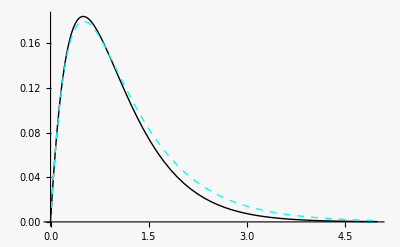
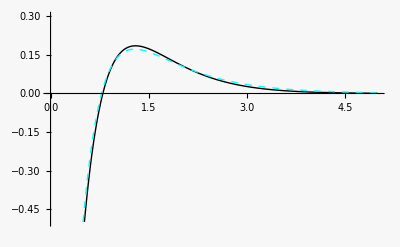

```mathematica
pars={k1->3,k2->4};
y1=OutputResponse[G1ss/.pars,DiracDelta[t],{t,0,tmax}];
y2=OutputResponse[G2ss,DiracDelta[t],{t,0,tmax}];
u1=OutputResponse[G1Kss/.pars,DiracDelta[t],{t,0,tmax}];
u2=OutputResponse[G2Kss,DiracDelta[t],{t,0,tmax}];

py1=Plot[y1,{t,0,tmax},PlotStyle ->{Thick,Black}];
py2=Plot[y2,{t,0,tmax},PlotStyle ->{Thick,Cyan,Dashed}];
pu1=Plot[u1,{t,0,tmax},PlotStyle ->{Thick,Black},PlotRange->{-0.5,0.3}];
pu2=Plot[u2,{t,0,tmax},PlotStyle ->{Thick,Cyan,Dashed},PlotRange->{-0.5,0.3}];


{Show[py1,py2],Show[pu1,pu2]}
```

```mathematica
OutputResponse[G1ss,DiracDelta[t],t]//FullSimplify//TraditionalForm
```

{(2 t ⅇ^(-(k2 t)/2) sinh(1/2 t √(-4 k1+k2^2-4)))/(√(-4 k1+k2^2-4))}

```mathematica
OutputResponse[G1Kss,DiracDelta[t],t]//FullSimplify//TraditionalForm
```

{t ⅇ^(-(k2 t)/2) (((k2^2-2 k1) sinh(1/2 t √(-4 k1+k2^2-4)))/(√(-4 k1+k2^2-4))-k2 cosh(1/2 t √(-4 k1+k2^2-4)))}

```mathematica
OutputResponse[G1ss/.k2->2 √(1+ k1),DiracDelta[t],t]//Simplify//TraditionalForm
```

{t t ⅇ^(-√(k1+1) t)}

```mathematica
OutputResponse[G1Kss/.k2->2 √(1+ k1),DiracDelta[t],t]//Simplify//TraditionalForm
```

{t ⅇ^(-√(k1+1) t) ((k1+2) t-2 √(k1+1))}

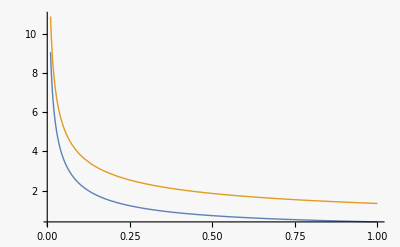

```mathematica
Plot[{ks1,ks2},{r,0.01,1}]
```